## Exact Solution

```mathematica
Clear["Global`*"]
```

```mathematica
cend = Compile[{{p,_Real}, {μ,_Real}},
 endϕ= SolveValues[(p^2 (ϕ/μ)^(-2+2 p))/(2 μ^2 (1-(ϕ/μ)^p)^2)==1,ϕ,Assumptions->{ϕ>0,ϕ<μ}]//N];
cini = Compile[{{p,_Real}, {μ,_Real}},endϕ = cend[p,μ];
iniϕ= SolveValues[(-ϕ^2+ϕi^2-(2 (ϕ^2 (ϕ/μ)^-p-ϕi^2 (ϕi/μ)^-p))/(-2+p))/(2 p)-60==0/.ϕ->endϕ,ϕi,Assumptions->{ϕi>0,ϕi<μ}]//N ];
```

## μ = 1

```mathematica
M:=0.0005167856358598168
p:= 4
μ:=1
ϕini =0.045514175860860345;
ϕend= 0.659399152881071;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0, 5 10^8}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

(*tprep = t/.FindRoot[ϕsr[t] ==ϕend,{t,10^8}];*)


Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1 = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,10^8},MaxSteps->1000];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds = Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend = t/.FindRoot[ϕ[t] ==ϕend,{t,10^8}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}]; 
(*pz[t_]:= a[t](pϕ[t](2-(a[t] ppa[t])/pa[t]^2) + (a[t] ppϕ[t])/pa[t])
ppz[t_]:= 2pa[t] pϕ[t]+(2a[t]pϕ[t]  ppa[t]^2)/pa[t]^3+ 4a[t] ppϕ[t] - (a[t]^2(2ppa[t] ppϕ[t] + pϕ[t] pppa[t]))/pa[t]^2 +a[t](-2 pϕ[t] ppa[t] +a[t] pppϕ[t])/pa[t]*)

conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,10^8},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t,10^8}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

h2 := 0.01
{{nS[0.05],r[0.05]},{nS[0.002],r[0.002]}}
```

InterpolatingFunction::dmval: Input value {1.1×10^9} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.×10^8} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.5×10^8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.28951×10^8} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.28950350627549×10^8} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2434082328333/9859} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

$Aborted

```mathematica
{{0.874379684637915,2.148445098398736*^-6},{4.235034541120699*^8,1.7831659400667304*^-6}}
```

```mathematica
{2079.953125,0.874379684637915}
```

```mathematica
{1790.453125,0.8655897787906143}
```

```mathematica
PS[0.05]
```

2.12085×10^-9

```mathematica
Timing[r[0.05]]
```

{4.90625,0.0549818}

## μ = 18

```mathematica
Mvalues = Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\data_ex\\mvalues_ex_k0002_N60.csv"];
```

```mathematica
p= 4
μ=4
M := Mvalues[[μ,2]]
ϕini =0.7064516737152218;
ϕend= 3.443139654313993;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,4 10^7}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,4  10^7}];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,  10^7}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}]; 
(*pz[t_]:= a[t](pϕ[t](2-(a[t] ppa[t])/pa[t]^2) + (a[t] ppϕ[t])/pa[t])
ppz[t_]:= 2pa[t] pϕ[t]+(2a[t]pϕ[t]  ppa[t]^2)/pa[t]^3+ 4a[t] ppϕ[t] - (a[t]^2(2ppa[t] ppϕ[t] + pϕ[t] pppa[t]))/pa[t]^2 +a[t](-2 pϕ[t] ppa[t] +a[t] pppϕ[t])/pa[t]*)

conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,4 10^7},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 5 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

h2 := 0.0005
{{nS[0.002],r[0.002]}}
```

4

4

NDSolve::mxst: Maximum number of 2122914 steps reached at the point t == 3.35814×10^7.

InterpolatingFunction::dmval: Input value {1.1×10^8} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {8.19971×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.91347×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.1×10^8} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {8.19971×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.91347×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.37291935294836×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.44260386928743×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

$Aborted

```mathematica
{{0.9665194828538834,0.017351905585683197}}
```

## Along μ II

```mathematica
Mvalues = Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\data_ex\\mvalues_ex_k005_N60.csv"];
```

### μ = 1

```mathematica
p= 4;
μ=1;
M=Mvalues[[μ,2]];
ϕini =First[cini[p,μ]];
ϕend= First[cend[p,μ]];

V[t_]= M^4(1 - (ϕs[t]/μ)^p);
Vp[t_] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,4.06 10^8}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];



Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1 = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0, 4.06 10^8},MaxSteps->1000000];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds = Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend = t/.FindRoot[ϕ[t] ==ϕend,{t,10^8}];
tend
z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}]; 

conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t,10^8}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

h2 := 0.00025
{nS[0.002],r[0.002]}
```

CompiledFunction::cfse: Compiled expression {0.0455142} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

InterpolatingFunction::dmval: Input value {1.1×10^9} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.2×10^9} lies outside the range of data in the interpolating function. Extrapolation will be used.

4.03329×10^8

{0.938095,1.80449×10^-6}

```mathematica
PS[0.05]
```

1.96729×10^-9

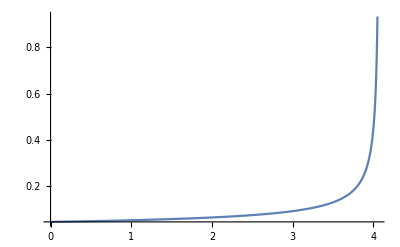

```mathematica
Plot[ϕ[t],{t,0,4.05 10^8},PlotRange->All]
```

### μ = 4

```mathematica
p= 4;
μ=4;
M=Mvalues[[μ,2]];
ϕini =First[cini[p,μ]];
ϕend= First[cend[p,μ]];

V[t_]= M^4(1 - (ϕs[t]/μ)^p);
Vp[t_] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,3.04 10^7}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];



Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1 = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0, 3.04 10^7},MaxSteps->1000000];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds = Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend = t/.FindRoot[ϕ[t] ==ϕend,{t,10^7}];
tend

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}]; 

conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

h2 := 0.00023
{nS[0.002],r[0.002]}
```

InterpolatingFunction::dmval: Input value {1.1×10^8} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {6.55335×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.33044×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

3.03668×10^7

{0.943027,0.00032659}

```mathematica
PS[0.05]
```

2.17053×10^-9

### μ = 5

```mathematica
p= 4;
μ=5;
M=Mvalues[[μ,2]];
ϕini =First[cini[p,μ]];
ϕend= First[cend[p,μ]];

V[t_]= M^4(1 - (ϕs[t]/μ)^p);
Vp[t_] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0, 2.1 10^7}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];



Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1 = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,2.1 10^7},MaxSteps->Infinity];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds = Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend = t/.FindRoot[ϕ[t] ==ϕend,{t,10^7}];
tend

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}]; 

conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t,10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

h2 := 0.00024
{nS[0.002],r[0.002]}
```

InterpolatingFunction::dmval: Input value {5.96926×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.45631×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.76844×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

2.08678×10^7

{0.947038,0.000704498}

```mathematica
PS[0.05]
```

2.17343×10^-9

### μ = 6

```mathematica
p= 4;
μ=6;
M=Mvalues[[μ,2]];
ϕini =First[cini[p,μ]];
ϕend= First[cend[p,μ]];

V[t_]= M^4(1 - (ϕs[t]/μ)^p);
Vp[t_] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0, 1.57 10^7}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];



Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1 = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,1.57 10^7},MaxSteps->1000000];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds = Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend = t/.FindRoot[ϕ[t] ==ϕend,{t,10^7}];
tend

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}]; 

conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t,10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

h2 := 0.00025
{nS[0.002],r[0.002]}
```

InterpolatingFunction::dmval: Input value {2.84396×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.21599×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.94289×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

1.56489×10^7

{0.947045,0.00127518}

```mathematica
PS[0.05]
```

2.16963×10^-9

### μ = 7

```mathematica
p= 4;
μ=7;
M=Mvalues[[μ,2]];
ϕini =First[cini[p,μ]];
ϕend= First[cend[p,μ]];

V[t_]= M^4(1 - (ϕs[t]/μ)^p);
Vp[t_] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,1.25 10^7}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];



Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1 = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0, 1.25 10^7},MaxSteps->1000000];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds = Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend = t/.FindRoot[ϕ[t] ==ϕend,{t,1.38 10^7}];
tend
z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}]; 

conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t,10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

h2 := 0.00023
{nS[0.002],r[0.002]}
```

InterpolatingFunction::dmval: Input value {1.38×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.35012×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.32525×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

1.24703×10^7

{0.95615,0.0020493}

```mathematica
PS[0.05]
```

2.16815×10^-9

### μ = 8

```mathematica
p= 4;
μ=8;
M=Mvalues[[μ,2]];
ϕini =First[cini[p,μ]];
ϕend= First[cend[p,μ]];

V[t_]= M^4(1 - (ϕs[t]/μ)^p);
Vp[t_] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,1.05 10^7}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];



Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1 = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,1.05 10^7},MaxSteps->100000];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds = Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend = t/.FindRoot[ϕ[t] ==ϕend,{t,10^7}];
tend

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}]; 

conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t,10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

h2 := 0.00023
{nS[0.002],r[0.002]}
```

InterpolatingFunction::dmval: Input value {1.05146×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

1.03874×10^7

{0.952366,0.00301443}

```mathematica
PS[0.05]
```

2.16655×10^-9

### μ = 9

```mathematica
p= 4;
μ=9;
M=Mvalues[[μ,2]];
ϕini =First[cini[p,μ]];
ϕend= First[cend[p,μ]];

V[t_]= M^4(1 - (ϕs[t]/μ)^p);
Vp[t_] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0, 9 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];



Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1 = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,9 10^6},MaxSteps->Infinity];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds = Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend = t/.FindRoot[ϕ[t] ==ϕend,{t,10^7}];
tend

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}]; 

conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t,10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

h2 := 0.001
{nS[0.002],r[0.002]}
```

InterpolatingFunction::dmval: Input value {1.×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.79721×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.63639×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

9.38714×10^6

InterpolatingFunction::dmval: Input value {9.38714×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.38705044242002×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.950761,0.00416251}

```mathematica
PS[0.002]
```

2.17399×10^-9

```mathematica
PS[0.05]
```

1.8769×10^-9

```mathematica
2.1651721989236128*^-9
```

### μ = 10

```mathematica
p= 4;
μ=10;
M=Mvalues[[μ,2]];
ϕini =First[cini[p,μ]];
ϕend= First[cend[p,μ]];

V[t_]= M^4(1 - (ϕs[t]/μ)^p);
Vp[t_] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0, 8.5 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];



Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1 = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,8.5 10^6}];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds = Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend = t/.FindRoot[ϕ[t] ==ϕend,{t,8.5 10^6}];
tend

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}]; 

conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},PrecisionGoal->1000,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t,10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

h2 := 0.00025
{nS[0.002],r[0.002]}
```

8.4524×10^6

{0.959743,0.00543638}

### μ = 11

```mathematica
p= 4;
μ=11;
M=Mvalues[[μ,2]];
ϕini =First[cini[p,μ]];
ϕend= First[cend[p,μ]];

V[t_]= M^4(1 - (ϕs[t]/μ)^p);
Vp[t_] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,7.8 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];



Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1 = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,7.8 10^6},MaxSteps->100000];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds = Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend = t/.FindRoot[ϕ[t] ==ϕend,{t,10^7}];
tend

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}]; 

conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,10^7},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t,10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

h2 := 0.001
{nS[0.002],r[0.002]}
```

InterpolatingFunction::dmval: Input value {8.4524×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.55971×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.20747×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

7.60401×10^6

InterpolatingFunction::dmval: Input value {7.84381281280674×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {8.08341138916155×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.954548,0.00682048}

### μ = 12

```mathematica
p= 4;
μ=12;
M=Mvalues[[μ,2]];
ϕini =First[cini[p,μ]];
ϕend= First[cend[p,μ]];

V[t_]= M^4(1 - (ϕs[t]/μ)^p);
Vp[t_] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,7 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];



Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1 = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,7 10^6},MaxSteps->100000];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds = Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend = t/.FindRoot[ϕ[t] ==ϕend,{t,10^7}];
tend

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}]; 

conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,10^7},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t,10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

h2 := 0.001
{nS[0.002],r[0.002]}
```

InterpolatingFunction::dmval: Input value {7.60401×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.39797×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {8.91624×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

6.95253×10^6

InterpolatingFunction::dmval: Input value {7.25747939200998×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7.56222612623109×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.957613,0.00827119}

### μ = 13

```mathematica
p= 4;
μ=13;
M=Mvalues[[μ,2]];
ϕini =First[cini[p,μ]];
ϕend= First[cend[p,μ]];

V[t_]= M^4(1 - (ϕs[t]/μ)^p);
Vp[t_] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0, 6.5 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];



Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1 = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,6.5 10^6},MaxSteps->100000];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds = Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend = t/.FindRoot[ϕ[t] ==ϕend,{t,10^7}];
tend

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}]; 

conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,10^7},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t,10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

h2 := 0.001
{nS[0.002],r[0.002]}
```

InterpolatingFunction::dmval: Input value {6.95253×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.28833×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {8.71863×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

6.44041×10^6

InterpolatingFunction::dmval: Input value {6.79656774605353×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {7.15252688538092×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{0.958842,0.00978315}

### μ = 20

```mathematica
p= 4;
μ=20;
M=Mvalues[[μ,2]];
ϕini =First[cini[p,μ]];
ϕend= First[cend[p,μ]];

V[t_]= M^4(1 - (ϕs[t]/μ)^p);
Vp[t_] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,4.20  10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];



Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1 = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,4.20 10^6},MaxSteps->1000000];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds = Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend = t/.FindRoot[ϕ[t] ==ϕend,{t,4 10^6}];
tend

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}]; 

conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t,10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

h2 := 0.001
{μ,nS[0.002],r[0.002]}
```

InterpolatingFunction::dmval: Input value {6.44041×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.97833×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.71058×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.69229×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

4.69213×10^6

InterpolatingFunction::dmval: Input value {4.69213×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.6920807589745×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{20,0.963858,0.0201692}

### μ = 30

```mathematica
p= 4;
μ=30;
M=Mvalues[[μ,2]];
ϕini =First[cini[p,μ]];
ϕend= First[cend[p,μ]];

V[t_]= M^4(1 - (ϕs[t]/μ)^p);
Vp[t_] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,3.88 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];



Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1 = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,3.88 10^6}];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds = Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend = t/.FindRoot[ϕ[t] ==ϕend,{t,10^6}];
tend

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}]; 

conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},PrecisionGoal->1000,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t,10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

h2 := 0.001
{μ,nS[0.002],r[0.002]}
```

InterpolatingFunction::dmval: Input value {6.27042×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.65283×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.21428×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

3.87848×10^6

{30,0.967728,0.0315338}

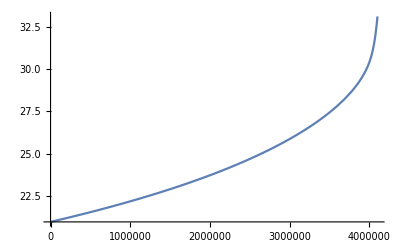

```mathematica
Plot[ϕ[t], {t,0, 4.1 10^6},PlotRange->All]
```

```mathematica
ϕend
```

29.3171

### μ = 35

```mathematica
p= 4;
μ=35;
M=Mvalues[[μ,2]];
ϕini =First[cini[p,μ]];
ϕend= First[cend[p,μ]];

V[t_]= M^4(1 - (ϕs[t]/μ)^p);
Vp[t_] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,3.70 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];



Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1 = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,3.7 10^6},MaxSteps->Infinity];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds = Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend = t/.FindRoot[ϕ[t] ==ϕend,{t,10^6}];
tend

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}]; 

conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t,10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

h2 := 0.0003
{μ,nS[0.002],r[0.002]}
```

InterpolatingFunction::dmval: Input value {5.71432×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {5.22177×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.86257×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

3.69063×10^6

{35,0.968084,0.035824}

### μ = 40

```mathematica
p= 4;
μ=40;
M=Mvalues[[μ,2]];
ϕini =First[cini[p,μ]];
ϕend= First[cend[p,μ]];

V[t_]= M^4(1 - (ϕs[t]/μ)^p);
Vp[t_] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,3.6 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];



Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1 = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,3.6 10^6},MaxSteps->Infinity];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds = Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend = t/.FindRoot[ϕ[t] ==ϕend,{t,10^6}];
tend

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}]; 

conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t,10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

h2 := 0.0005
{μ,nS[0.002],r[0.002]}
```

InterpolatingFunction::dmval: Input value {5.34387×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.92918×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.62084×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

3.56069×10^6

{40,0.968468,0.0392623}

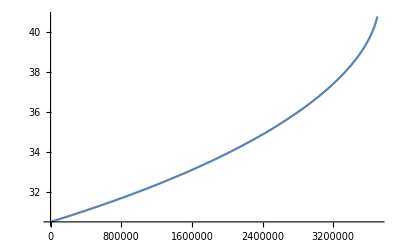

```mathematica
Plot[ϕ[t], {t,0,3.7 10^6}]
```

### μ = 50

```mathematica
p= 4;
μ=50;
M=Mvalues[[μ,2]];
ϕini =First[cini[p,μ]];
ϕend= First[cend[p,μ]];

V[t_]= M^4(1 - (ϕs[t]/μ)^p);
Vp[t_] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,3.5 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];



Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1 = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,3.5 10^6},MaxSteps->Infinity];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds = Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend = t/.FindRoot[ϕ[t] ==ϕend,{t,3 10^6}];
tend

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}]; 

conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->10,PrecisionGoal->∞,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t,10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

h2 := 0.0005
{μ,nS[0.002],r[0.002]}
```

InterpolatingFunction::dmval: Input value {3.50701×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

3.39405×10^6

NDSolve::ndtol: Tolerances requested by the AccuracyGoal and PrecisionGoal options could not be achieved at t == 207445.573589055.

InterpolatingFunction::dmval: Input value {207.795} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{50,1.0298,0.0445172}

### μ = 60

```mathematica
p= 4;
μ=60;
M=Mvalues[[μ,2]];
ϕini =First[cini[p,μ]];
ϕend= First[cend[p,μ]];

V[t_]= M^4(1 - (ϕs[t]/μ)^p);
Vp[t_] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,3.3 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];



Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1 = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,3.3 10^6},MaxSteps->Infinity];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds = Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend = t/.FindRoot[ϕ[t] ==ϕend,{t,3 10^6}];
tend

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}]; 

conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->10,PrecisionGoal->10,WorkingPrecision->15,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t,10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

h2 := 0.0001
{μ,nS[0.002],r[0.002]}
```

InterpolatingFunction::dmval: Input value {3.36226×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.30242×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

3.29256×10^6

{60,0.968961,0.0483315}

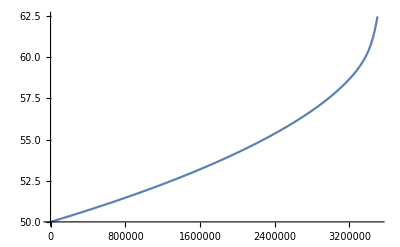

```mathematica
Plot[ϕ[t],{t,0,3.5 10^6}]
```

### μ = 70

```mathematica
p= 4;
μ=70;
M=Mvalues[[μ,2]];
ϕini =First[cini[p,μ]];
ϕend= First[cend[p,μ]];

V[t_]= M^4(1 - (ϕs[t]/μ)^p);
Vp[t_] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,3.25 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];



Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1 = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,3.25 10^6},MaxSteps->Infinity];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds = Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend = t/.FindRoot[ϕ[t] ==ϕend,{t,3.2 10^6}];
tend

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}]; 

conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},PrecisionGoal->1000,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t,10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

h2 := 0.001
{nS[0.002],r[0.002]}
```

CompiledFunction::cfse: Compiled expression {69.3035} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression {59.8786} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression {69.3035} should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfse will be suppressed during this calculation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfex will be suppressed during this calculation.

CompiledFunction::cfse: Compiled expression {69.3035} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

3.22463×10^6

{0.967463,0.0511778}

### μ = 80

```mathematica
p= 4;
μ=80;
M=Mvalues[[μ,2]];
ϕini =First[cini[p,μ]];
ϕend= First[cend[p,μ]];

V[t_]= M^4(1 - (ϕs[t]/μ)^p);
Vp[t_] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0,3.25 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];



Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1 = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0,3.25  10^6},MaxSteps->Infinity];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds = Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend = t/.FindRoot[ϕ[t] ==ϕend,{t,3 10^6}];
tend

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}]; 

conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},MaxSteps->Infinity,InterpolationOrder->All,PrecisionGoal->1000,WorkingPrecision->MachinePrecision];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t,10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

h2 := 0.001
{nS[0.002],r[0.002]}
```

3.17611×10^6

{0.966363,0.0534089}

```mathematica
M
```

0.00800613

```mathematica
PS[0.002]
```

```mathematica
2.126285284833542*^-9
```

```mathematica
2.126285284833542*^-9
```

```mathematica
2.118650547056334*^-9
```

```mathematica
Plot[{z[t],a[t]}, {t,0,  tend}]
```

-Graphics-

## Data

### h2 = 0.00025, k_M = 0.05

```mathematica
{{0.9380949933386546,1.8044868895151993*^-6},(*1*)
{0.9430272786364086,0.000326589689756389},(*4*)
{0.9472257936217712,0.0007044976082558171},(*5*)
{0.9470454729475886,0.0012751808540733783},(*6*)
{0.9561500828235727,0.0020492986376870314},(*7*)
{0.9523656858021129,0.003014427603946156},(*8*)






}
```

### Optimal discretization (h2 = 0.001)

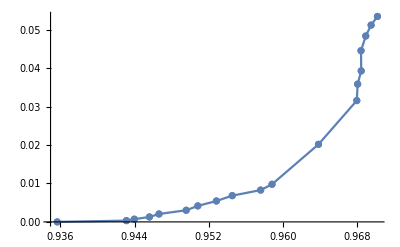

```mathematica
{{0.9356503293312525,1.811782338244197*^-6}, (*1*)
{0.9431224967234402,0.0003283845616181333},  (*4*)
{0.9439733711495162,0.0007065207599182795}, (*5*)
{0.9456071223223051,0.0012806022726872686}, (*6*)
{0.9466390577682396,0.002055560122590277}, (*7*)
{0.9495782374138713,0.003025081714597308},(*8*)
{0.95083319551492,0.004161344023930173},(*9*)
{0.9528347221658233,0.005435973160998737},(*10*)
{0.9545481365719721,0.0068204828363355495}, (*11*)
{0.9576133238664827,0.008271188798865034},(*12*)
{0.9588423419566543,0.00978315393835428},(*13*)

{0.9638576339244892,0.02016918649669537},(*20*)
{0.9679927066989275,0.03154066146959764},(*30*)
{0.9680837917130259,0.035824027832161216},(*35*)
{0.968468278554595,0.039262326336825706},(*40*)
{0.9684493760886753,0.04451386987717267},(*50*)
{0.9689606129350525,0.04833145105591246},(*60*)
{0.9695378313220716,0.051172239394541866},(*70*)
{0.9702238525760034,0.05341515009858991},(*80*)
}//ListPlot[#,Joined->True,Mesh->Full]&
```

### Non optimal discretization

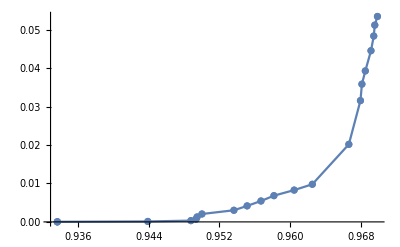

```mathematica
{{0.933674770665307,1.811782338244197*^-6},
{0.9337023883885912,0.000025683640140358735},
{0.943906758508377,0.00011672457080225098},(**)
{0.9487719678080978,0.0003283845616181333},(*4*)
{0.9493505676961282,0.0007065207599182795},(*5*)
{0.9494698385663891,0.0012806022726872686},(*6*)
{0.9500208347010771,0.002055560122590277},(*7*)
{0.9536268314482502,0.003025081714597308}, (*8*)
{0.9551202330648172,0.004161344023930173},(*9*)
{0.9566862154183613,0.005435973160998737},
{0.9581496758596721,0.0068204828363355495},(*11*)
{0.9604324703543105,0.008271188798865034},(*12*)
{0.962482667915322,0.00978315393835428},(*13*)
{0.9666079035681824,0.02016918649669537},
{0.9679189454680301,0.03154027752732573},
{0.9680837917130259,0.035824027832161216},(*35*)
{0.968468278554595,0.039262326336825706},
{0.9691080541476893,0.04451386987717267},
{0.9694207795605173,0.04833145105591246},
{0.9695378313220716,0.051172239394541866},
{0.969839525288756,0.05342090866837186}




 }//ListPlot[#,Joined->True,Mesh->Full]&
```

## Analysis stability of derivative

### μ =1

```mathematica
Table[{ h2 = i,nS[0.002] },{i, 0.0001, 0.001, 0.0001}]
```

{{0.0001,0.93565},{0.0002,0.940303},{0.0003,0.937122},{0.0004,0.932183},{0.0005,0.933675},{0.0006,0.93217},{0.0007,0.933098},{0.0008,0.931448},{0.0009,0.931603},{0.001,0.929679}}

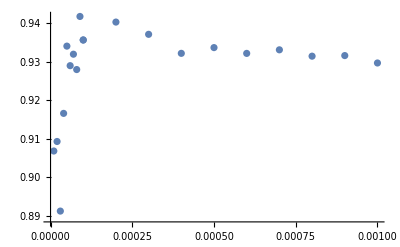

```mathematica
{{0.00001,0.9068256027240115},{0.00002,0.9092968763725993},{0.000030000000000000004,0.8912264726921797},{0.00004,0.9165946231492705},{0.00005,0.9340574925542064},{0.00006,0.9289837430727513},{0.00007000000000000001,0.9319576810784138},{0.00008,0.9279748294379757},{0.00009,0.9417600091056159},{0.0001,0.9356503293312525},{0.0001,0.9356503293312525},{0.0002,0.9403027956992447},{0.00030000000000000003,0.937122319925267},{0.0004,0.9321829591931055},{0.0005,0.933674770665307},{0.0006000000000000001,0.9321703864455853},{0.0007000000000000001,0.9330980712889294},{0.0008,0.9314481484826523},{0.0009000000000000001,0.9316029985311518},{0.001,0.9296792303870858}}//ListPlot
```

Apparently better for values of h2 higher that 0.0001 till 0.001 when it reaches the order of the value of k = 0.002

### μ = 10

```mathematica
Table[{ h2 = i,nS[0.002] },{i, 0.0001, 0.001, 0.0001}]
```

{{0.0001,0.956144},{0.0002,0.959155},{0.0003,0.954299},{0.0004,0.955285},{0.0005,0.956686},{0.0006,0.954226},{0.0007,0.954661},{0.0008,0.954345},{0.0009,0.953479},{0.001,0.952835}}

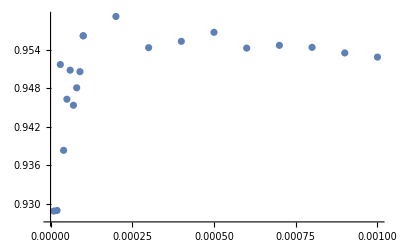

```mathematica
{{0.00001,0.9288648908395716},{0.00002,0.9289616963789146},{0.000030000000000000004,0.9516721302508615},{0.00004,0.9383173400252658},{0.00005,0.9462738405174456},{0.00006,0.9507969005822305},{0.00007000000000000001,0.9453360399273849},{0.00008,0.9480501138915705},{0.00009,0.9505642621645056},{0.0001,0.9561438141376228},{0.0001,0.9561438141376228},{0.0002,0.9591550687277837},{0.00030000000000000003,0.9542985429439469},{0.0004,0.9552851001236398},{0.0005,0.9566862154183613},{0.0006000000000000001,0.9542263643253059},{0.0007000000000000001,0.9546607779749606},{0.0008,0.9543454106567537},{0.0009000000000000001,0.9534785812233022},{0.001,0.9528347221658233}}//ListPlot
```

Apparently better for values of h2 higher that 0.0001 till 0.001 when it reaches the order of the value of k = 0.002

### μ = 20

```mathematica
Table[{ h2 = i,nS[0.002] },{i, 0.0001, 0.001, 0.0001}]
```

{{0.0001,0.969485},{0.0002,0.965288},{0.0003,0.966496},{0.0004,0.968154},{0.0005,0.966608},{0.0006,0.966175},{0.0007,0.966735},{0.0008,0.965755},{0.0009,0.964127},{0.001,0.963858}}

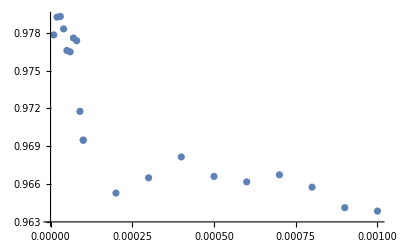

```mathematica
{{0.00001,0.9778356444254901},{0.00002,0.979247955260924},{0.000030000000000000004,0.9793006334452948},{0.00004,0.9783135093571673},{0.00005,0.9766022378428604},{0.00006,0.9764939757758682},{0.00007000000000000001,0.9775895712985078},{0.00008,0.9773740987695532},{0.00009,0.9717684719171341},{0.0001,0.9694854261004523},{0.0001,0.9694854261004523},{0.0002,0.9652881777994181},{0.00030000000000000003,0.9664959373822987},{0.0004,0.9681544937036036},{0.0005,0.9666079035681824},{0.0006000000000000001,0.96617510620582},{0.0007000000000000001,0.9667353274666429},{0.0008,0.9657550566784391},{0.0009000000000000001,0.9641266497565161},{0.001,0.9638576339244892}}//ListPlot
```

Apparently better for values of h2 higher that 0.0001 till 0.001 when it reaches the order of the value of k = 0.002

### μ = 30

```mathematica
Table[{ h2 = i,nS[0.002] },{i, 0.0001, 0.001, 0.0001}]
```

{{0.0001,0.966486},{0.0002,0.967597},{0.0003,0.972356},{0.0004,0.967836},{0.0005,0.969592},{0.0006,0.970348},{0.0007,0.969239},{0.0008,0.96793},{0.0009,0.969449},{0.001,0.968133}}

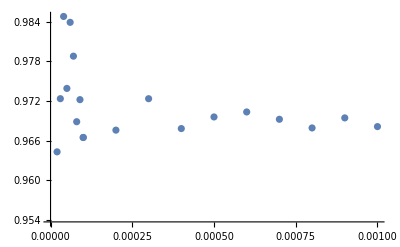

```mathematica
{{0.00001,0.9023993986858653},{0.00002,0.9643127867246816},{0.000030000000000000004,0.972357895227148},{0.00004,0.9848001418392235},{0.00005,0.9739109142117093},{0.00006,0.9839116342595275},{0.00007000000000000001,0.9787907141640921},{0.00008,0.9688725338236133},{0.00009,0.9722119999850045},{0.0001,0.9664855590752041},{0.0001,0.9664855590752041},{0.0002,0.967597478479638},{0.00030000000000000003,0.9723560576265812},{0.0004,0.9678355833318518},{0.0005,0.9695920008311231},{0.0006000000000000001,0.9703484051140057},{0.0007000000000000001,0.9692385805096883},{0.0008,0.9679295998633047},{0.0009000000000000001,0.9694490838252379},{0.001,0.9681331406238194}}//ListPlot
```

Apparently better for values of h2 higher that 0.0001 till 0.001 when it reaches the order of the value of k = 0.002

### μ = 40

```mathematica
Table[{ h2 = i,nS[0.002] },{i, 0.0001, 0.001, 0.0001}]
```

{{0.0001,0.968586},{0.0002,0.973893},{0.0003,0.966733},{0.0004,0.967889},{0.0005,0.968468},{0.0006,0.967869},{0.0007,0.968969},{0.0008,0.967659},{0.0009,0.96555},{0.001,0.966066}}

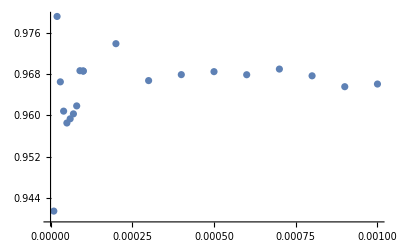

```mathematica
{{0.00001,0.94142322300818},{0.00002,0.9791716535302918},{0.000030000000000000004,0.9664881033404299},{0.00004,0.9608079249978109},{0.00005,0.9585094133064911},{0.00006,0.959320336018882},{0.00007000000000000001,0.9602785656984116},{0.00008,0.961823440551656},{0.00009,0.9686485834803398},{0.0001,0.9685858000628453},{0.0001,0.9685858000628453},{0.0002,0.9738926041059549},{0.00030000000000000003,0.9667329080238638},{0.0004,0.9678890953066331},{0.0005,0.968468278554595},{0.0006000000000000001,0.967869014357837},{0.0007000000000000001,0.968968838383255},{0.0008,0.9676590453366594},{0.0009000000000000001,0.9655497191869694},{0.001,0.9660656585449217}}//ListPlot
```

### μ = 50

```mathematica
Table[{ h2 = i,nS[0.002] },{i, 0.0001, 0.001, 0.0001}]
```

{{0.0001,0.972398},{0.0002,0.970228},{0.0003,0.971078},{0.0004,0.970891},{0.0005,0.969108},{0.0006,0.970756},{0.0007,0.968722},{0.0008,0.968449},{0.0009,0.96834},{0.001,0.966407}}

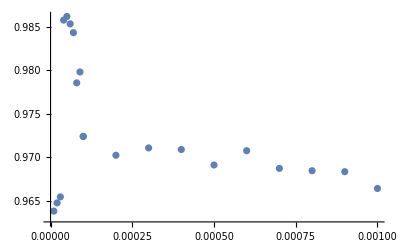

```mathematica
{{0.00001,0.9638042041002798},{0.00002,0.9647437109081872},{0.000030000000000000004,0.9654399445393436},{0.00004,0.985783410369778},{0.00005,0.9862057259627204},{0.00006,0.9853508633291064},{0.00007000000000000001,0.9843448678696592},{0.00008,0.9785662338323808},{0.00009,0.9798167214573886},{0.0001,0.9723980949408002},{0.0001,0.9723980949408002},{0.0002,0.9702282566039945},{0.00030000000000000003,0.9710776863761595},{0.0004,0.9708908038646503},{0.0005,0.9691080541476893},{0.0006000000000000001,0.9707555660078677},{0.0007000000000000001,0.9687215617595865},{0.0008,0.9684493760886753},{0.0009000000000000001,0.9683395156208627},{0.001,0.966406744660462}}//ListPlot
```

### μ = 60

```mathematica
Table[{ h2 = i,nS[0.002] },{i, 0.0001, 0.001, 0.0001}]
```

{{0.0001,0.968961},{0.0002,0.97335},{0.0003,0.969392},{0.0004,0.969421},{0.0005,0.968182},{0.0006,0.968503},{0.0007,0.969403},{0.0008,0.968086},{0.0009,0.967747},{0.001,0.968595}}

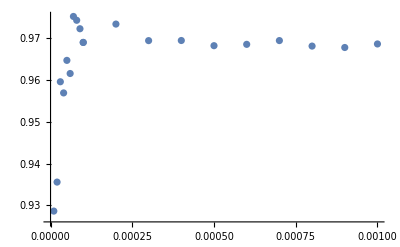

```mathematica
{{0.00001,0.9286212852705955},{0.00002,0.9355569655493258},{0.000030000000000000004,0.9595535758572533},{0.00004,0.9568825262080402},{0.00005,0.9646687606750253},{0.00006,0.9615265404802532},{0.00007000000000000001,0.9751720225126183},{0.00008,0.9742579583042189},{0.00009,0.9722332542354792},{0.0001,0.9689606129350525},{0.0001,0.9689606129350525},{0.0002,0.9733502455988922},{0.00030000000000000003,0.9693920568365375},{0.0004,0.9694207795605173},{0.0005,0.9681819332307205},{0.0006000000000000001,0.9685027819071892},{0.0007000000000000001,0.9694032172090518},{0.0008,0.9680863007971321},{0.0009000000000000001,0.9677470984658778},{0.001,0.9685953926018305}}//ListPlot
```

### μ = 70

```mathematica
Table[{ h2 = i,nS[0.002] },{i, 0.0001, 0.001, 0.0001}]
```

{{0.0001,0.973099},{0.0002,0.972962},{0.0003,0.974028},{0.0004,0.971149},{0.0005,0.971563},{0.0006,0.970323},{0.0007,0.969833},{0.0008,0.969251},{0.0009,0.96799},{0.001,0.967287}}

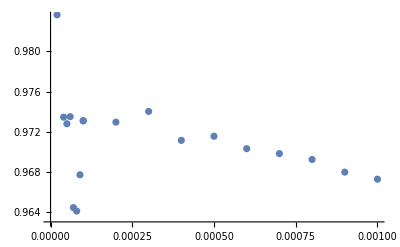

```mathematica
{{0.00001,1.0025354519654652},{0.00002,0.9836313797856853},{0.000030000000000000004,0.9857062029183091},{0.00004,0.9734592524370211},{0.00005,0.9728014149241085},{0.00006,0.9735082734988045},{0.00007000000000000001,0.9644624149267823},{0.00008,0.9641159283571838},{0.00009,0.9677291183938832},{0.0001,0.9730986092585203},{0.0001,0.9730986092585203},{0.0002,0.9729619942392654},{0.00030000000000000003,0.9740275493779381},{0.0004,0.9711489163841116},{0.0005,0.9715629740613824},{0.0006000000000000001,0.9703232707066153},{0.0007000000000000001,0.9698333307078186},{0.0008,0.9692505719613069},{0.0009000000000000001,0.9679895256911235},{0.001,0.9672872871951321}}//ListPlot
```

### μ =80

```mathematica
Table[{ h2 = i,nS[0.002] },{i, 0.0001, 0.001, 0.0001}]
```

{{0.0001,0.971032},{0.0002,0.972363},{0.0003,0.973424},{0.0004,0.969632},{0.0005,0.96984},{0.0006,0.969229},{0.0007,0.967235},{0.0008,0.967794},{0.0009,0.967979},{0.001,0.966401}}

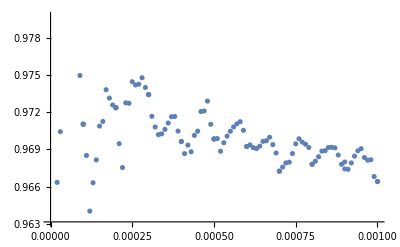

```mathematica
{{0.00001,0.9863637719225229},{0.00002,0.9663318317669977},{0.000030000000000000004,0.9704288802032056},{0.00004,0.9811244020478347},{0.00005,0.9809520410565625},{0.00006,0.9852082296186496},{0.00007000000000000001,0.9824238824727002},{0.00008,0.9819507284562434},{0.00009,0.9749667741717275},{0.0001,0.9710320371114158},{0.0001,0.9710320371114158},{0.0002,0.9723625758874243},{0.00030000000000000003,0.9734237299921604},{0.0004,0.9696317793338891},{0.0005,0.969839525288756},{0.0006000000000000001,0.9692293036831431},{0.0007000000000000001,0.9672353387212886},{0.0008,0.9677940021194558},{0.0009000000000000001,0.9679793734414951},{0.001,0.9664009449046336},{0.0001,0.9710320371114158},{0.00011,0.9685074559471005},{0.00012,0.9640143845105029},{0.00013000000000000002,0.9663017063320699},{0.00014000000000000001,0.9681495273898046},{0.00015000000000000001,0.9708803771365483},{0.00016,0.9712566082410109},{0.00017,0.9738201235596311},{0.00018,0.9731406891325378},{0.00019,0.9725855429000552},{0.0002,0.9723625758874243},{0.0002,0.9723625758874243},{0.00021,0.9694565630098465},{0.00022,0.9675323549345379},{0.00023,0.9727546874347123},{0.00024,0.9727222008478564},{0.00025,0.9744628762494021},{0.00026000000000000003,0.9742016875231778},{0.00027,0.9742660898759249},{0.00028000000000000003,0.9747845787082885},{0.00029,0.9739999860411893},{0.00030000000000000003,0.9734237299921604},{0.0003,0.9734237299921604},{0.00031,0.9716674289410142},{0.00031999999999999997,0.9708061525717554},{0.00033,0.9701908046162385},{0.00033999999999999997,0.9702509970119932},{0.00035,0.9706168597010277},{0.00035999999999999997,0.9711269100654443},{0.00037,0.97163553181169},{0.00037999999999999997,0.9716554722471974},{0.00039,0.9704767566764144},{0.00039999999999999996,0.9696317793338891},{0.00041,0.9686532271238467},{0.00042,0.9693416944112718},{0.00043,0.9688044106272151},{0.00043999999999999996,0.9701293852529311},{0.00045,0.9704715628300651},{0.00046,0.9720595320239525},{0.00047,0.9721000036998979},{0.00047999999999999996,0.972899636974871},{0.00049,0.9710229635141089},{0.0005,0.969839525288756},{0.0005,0.969839525288756},{0.00051,0.969872604642644},{0.0005200000000000001,0.9688486985785042},{0.00053,0.9695323006802772},{0.00054,0.9700696039572988},{0.00055,0.9704613746444015},{0.0005600000000000001,0.9708129510678005},{0.00057,0.9710631659155902},{0.00058,0.9712360860291883},{0.00059,0.9705374821075188},{0.0006000000000000001,0.9692293036831431},{0.00061,0.969360666570586},{0.00062,0.969136536867217},{0.00063,0.969064975147062},{0.00064,0.9692620152997385},{0.00065,0.96964403606535},{0.00066,0.9696920495428692},{0.00067,0.9699772744751939},{0.00068,0.9693842090797833},{0.0006900000000000001,0.968706617667209},{0.0007,0.9672353387212886},{0.00071,0.9675688348813555},{0.00072,0.9679069178478402},{0.00073,0.9679657876730704},{0.00074,0.9686634297077008},{0.00075,0.9694445955477582},{0.00076,0.9698549843548379},{0.0007700000000000001,0.9695833464628302},{0.0007800000000000001,0.9694133914538828},{0.00079,0.969148638851252},{0.0008,0.9677940021194558},{0.00081,0.9680463737885344},{0.00082,0.9684039864154782},{0.00083,0.9688579230742732},{0.00084,0.9688919490996695},{0.0008500000000000001,0.9691503979929015},{0.0008600000000000001,0.9691678857839838},{0.0008700000000000001,0.9691235571981203},{0.00088,0.9685420558763609},{0.0008900000000000001,0.9677933913239745},{0.0009,0.9674227942973488},{0.00091,0.9673895960028711},{0.00092,0.9679027943177569},{0.00093,0.9684507035417333},{0.0009400000000000001,0.9688850107158041},{0.0009500000000000001,0.9690554527754346},{0.00096,0.9683426850115844},{0.00097,0.9681252374183014},{0.00098,0.9681609436511599},{0.00099,0.9668050634537433},{0.001,0.9664009449046336}}//ListPlot[#]&
```

### μ = 80 with other discretization of ϕ

```mathematica
sssa = Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.002, 0.00001}];
```

InterpolatingFunction::dmval: Input value {-2310.95} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-3040.02} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-3689.08} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == -191.617, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

RowReduce::mindet: Input matrix contains an indeterminate entry.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

RowReduce::mindet: Input matrix contains an indeterminate entry.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

RowReduce::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of RowReduce::mindet will be suppressed during this calculation.

```mathematica
ListPlot[sssa]
```

-Graphics-

```mathematica
stabilityderivative={};
Do[der = (sssa[[t+1,2]]- sssa[[t-1, 2]])/(sssa[[t+1,1]] - sssa[[t-1, 1]]); AppendTo[stabilityderivative,{sssa[[t,1]], Abs[der]}],{t,2, Length[sssa]-2}]
```

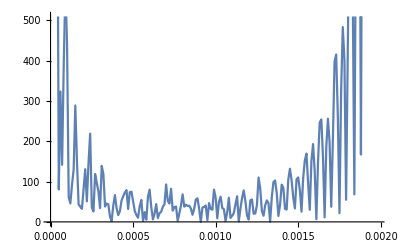

```mathematica
stabilityderivative//ListPlot[#,Joined->True]&
```

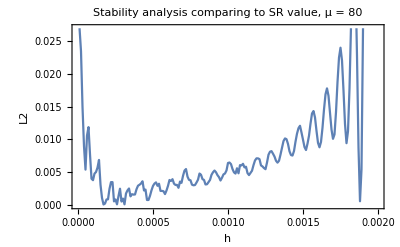

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] - 0.9727820282000144)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 80 ", Frame->True, FrameLabel->{"h","L2"}]
```

### μ = 70 with other discretization of ϕ

```mathematica
sssa = Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.002, 0.00001}];
```

InterpolatingFunction::dmval: Input value {-5025.43} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5321.16} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-5576.7} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == -198.072, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

RowReduce::mindet: Input matrix contains an indeterminate entry.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

RowReduce::mindet: Input matrix contains an indeterminate entry.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

RowReduce::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of RowReduce::mindet will be suppressed during this calculation.

```mathematica
ListPlot[sssa]
```

-Graphics-

```mathematica
stabilityderivative={};
Do[der = (sssa[[t+1,2]]- sssa[[t-1, 2]])/(sssa[[t+1,1]] - sssa[[t-1, 1]]); AppendTo[stabilityderivative,{sssa[[t,1]], Abs[der]}],{t,2, Length[sssa]-2}]
```

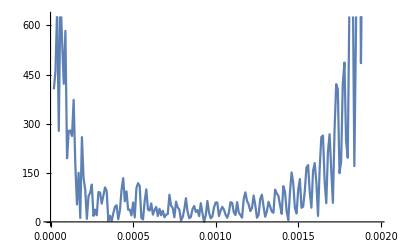

```mathematica
stabilityderivative//ListPlot[#,Joined->True]&
```

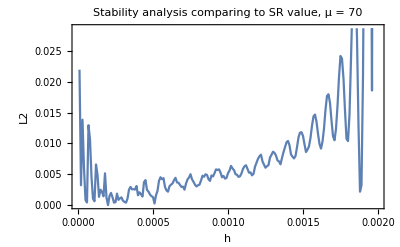

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] - 0.9726401920618747)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 70 ", Frame->True, FrameLabel->{"h","L2"}]
```

### μ = 10 with other discretization of ϕ

```mathematica
sssa = Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.002, 0.00001}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-47356.3} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-60512.8} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-73524.6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

RowReduce::mindet: Input matrix contains an indeterminate entry.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

RowReduce::mindet: Input matrix contains an indeterminate entry.

NDSolve::ndsz: At t == -1113.45, step size is effectively zero; singularity or stiff system suspected.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

RowReduce::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of RowReduce::mindet will be suppressed during this calculation.

NDSolve::ndsz: At t == -1113.45, step size is effectively zero; singularity or stiff system suspected.

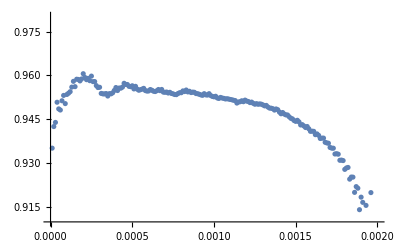

```mathematica
ListPlot[sssa]
```

```mathematica
stabilityderivative={};
Do[der = (sssa[[t+1,2]]- sssa[[t-1, 2]])/(sssa[[t+1,1]] - sssa[[t-1, 1]]); AppendTo[stabilityderivative,{sssa[[t,1]], Abs[der]}],{t,2, Length[sssa]-2}]
```

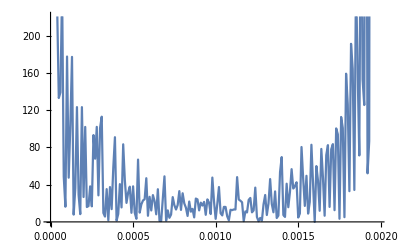

```mathematica
stabilityderivative//ListPlot[#,Joined->True]&
```

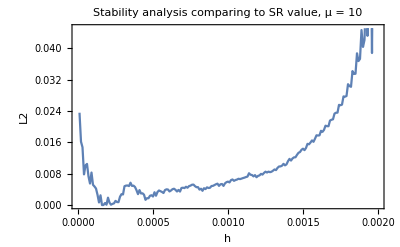

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] - 0.9586451978846227)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 10 ", Frame->True, FrameLabel->{"h","L2"}]
```

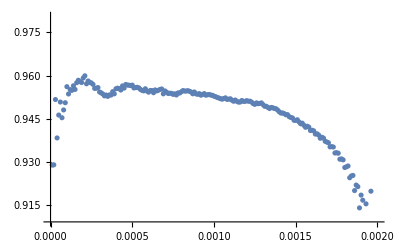

```mathematica
ListPlot[sssa]
```

```mathematica
stabilityderivative={};
Do[der = (sssa[[t+1,2]]- sssa[[t-1, 2]])/(sssa[[t+1,1]] - sssa[[t-1, 1]]); AppendTo[stabilityderivative,{sssa[[t,1]], Abs[der]}],{t,2, Length[sssa]-2}]
```

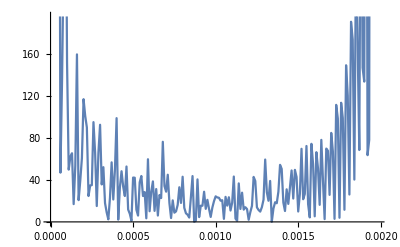

```mathematica
stabilityderivative//ListPlot[#,Joined->True]&
```

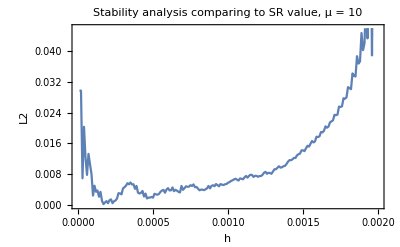

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] - 0.9586451978846227)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 10 ", Frame->True, FrameLabel->{"h","L2"}]
```

### μ = 30 with other discretization of ϕ

```mathematica
sssa = Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.002, 0.00001}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-16136.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-18034.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-19788.5} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == -287.888, step size is effectively zero; singularity or stiff system suspected.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

RowReduce::mindet: Input matrix contains an indeterminate entry.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

RowReduce::mindet: Input matrix contains an indeterminate entry.

NDSolve::ndsz: At t == -287.888, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

RowReduce::mindet: Input matrix contains an indeterminate entry.

General::stop: Further output of RowReduce::mindet will be suppressed during this calculation.

```mathematica
ListPlot[sssa]
```

-Graphics-

```mathematica
stabilityderivative={};
Do[der = (sssa[[t+1,2]]- sssa[[t-1, 2]])/(sssa[[t+1,1]] - sssa[[t-1, 1]]); AppendTo[stabilityderivative,{sssa[[t,1]], Abs[der]}],{t,2, Length[sssa]-2}]
```

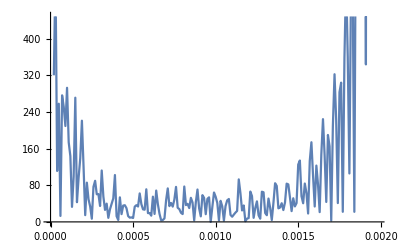

```mathematica
stabilityderivative//ListPlot[#,Joined->True]&
```

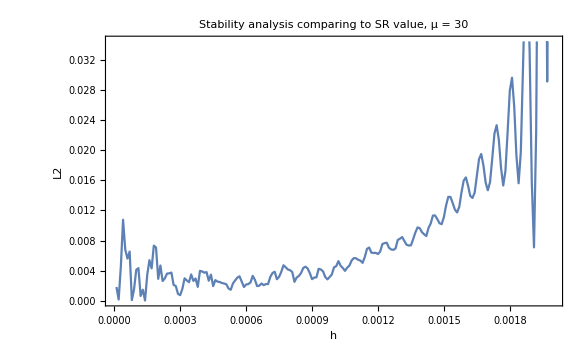

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] - 0.9721619409958305)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 30 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
ListPlot[sssa]
```

-Graphics-

```mathematica
stabilityderivative={};
Do[der = (sssa[[t+1,2]]- sssa[[t-1, 2]])/(sssa[[t+1,1]] - sssa[[t-1, 1]]); AppendTo[stabilityderivative,{sssa[[t,1]], Abs[der]}],{t,2, Length[sssa]-2}]
```

```mathematica
stabilityderivative//ListPlot[#,Joined->True]&
```

-Graphics-

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] - 0.9586451978846227)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 10 ", Frame->True, FrameLabel->{"h","L2"}]
```

-Graphics-

## Prueba μ = 4

```mathematica
Mvalues = Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\data_ex\\mvalues_ex_k005_N60.csv"];
```

```mathematica
Mvalues[[4,2]]
```

0.00188506

```mathematica
Clear["Global`*"]
```

```mathematica
p= 4;
μ=4;
M := 0.0018850574173281628
ϕini =0.7064516737152218;
ϕend= 3.443139654313993;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0, 3.08 10^7}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0, 3.08 10^7},MaxStepSize->10000,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,  10^7}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

InterpolatingFunction::dmval: Input value {1.1×10^8} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {6.55335×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.33044×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

### μ = 4 with other discretization of ϕ, step 100

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.002, 0.00001}]];
```

InterpolatingFunction::dmval: Input value {-221546.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-241.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2661.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == -3695.8, step size is effectively zero; singularity or stiff system suspected.

```mathematica
ListPlot[sssa]
```

-Graphics-

```mathematica
stabilityderivative={};
Do[der = (sssa[[t+1,2]]- sssa[[t-1, 2]])/(sssa[[t+1,1]] - sssa[[t-1, 1]]); AppendTo[stabilityderivative,{sssa[[t,1]], Abs[der]}],{t,2, Length[sssa]-2}]
```

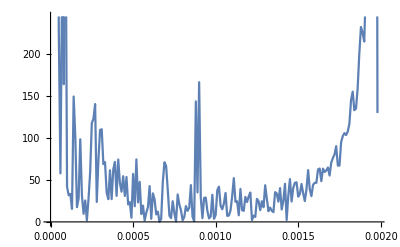

```mathematica
stabilityderivative//ListPlot[#,Joined->True]&
```

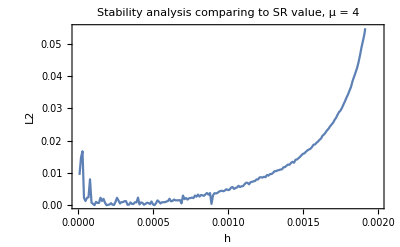

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9480646011892383)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 4 ", Frame->True, FrameLabel->{"h","L2"}]
```

```mathematica
ϕ[t]
```

InterpolatingFunction[…][t]

## Prueba μ = 20

```mathematica
Mvalues = Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\data_ex\\mvalues_ex_k005_N60.csv"];
```

```mathematica
Mvalues[[20,2]]
cini[4,20]
cend[4,20]
```

0.00535731

CompiledFunction::cfse: Compiled expression {19.3287} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

CompiledFunction::cfse: Compiled expression {11.838} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

{11.838}

{19.3287}

```mathematica
Clear["Global`*"]
```

```mathematica
p= 4;
μ=20;
M := 0.005357305723288271
ϕini =11.838012784632001;
ϕend= 19.328683873439395;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0, 4.55 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0, 4.55 10^6}, MaxStepSize->1000,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,  5 10^6}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

InterpolatingFunction::dmval: Input value {5.×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.90288×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.82386×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
tend
```

4.43099×10^6

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

### μ = 20 with other discretization of ϕ

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.002, 0.00001}]];
```

InterpolatingFunction::dmval: Input value {-3597.35} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-6200.6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-8611.74} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == -323.657, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == -488.511, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

```mathematica
ListPlot[sssa]
```

-Graphics-

```mathematica
stabilityderivative={};
Do[der = (sssa[[t+1,2]]- sssa[[t-1, 2]])/(sssa[[t+1,1]] - sssa[[t-1, 1]]); AppendTo[stabilityderivative,{sssa[[t,1]], Abs[der]}],{t,2, Length[sssa]-2}]
```

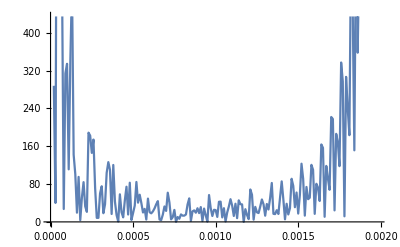

```mathematica
stabilityderivative//ListPlot[#,Joined->True]&
```

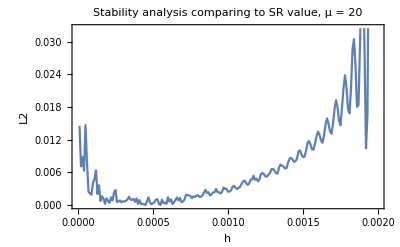

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9672887073997047)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 20 ", Frame->True, FrameLabel->{"h","L2"}]
```

## Prueba μ = 50

```mathematica
Mvalues = Import["C:\\Users\\RAUL\\Documents\\Wolfram Mathematica\\Titulation - Cosmology\\data_ex\\mvalues_ex_k005_N60.csv"];
```

```mathematica
Mvalues[[50,2]]
cini[4,50]
cend[4,50]
```

0.00721617

CompiledFunction::cfse: Compiled expression {40.2141} should be a machine-size real number.

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

{40.2141}

{49.3076}

```mathematica
Clear["Global`*"]
```

```mathematica
p= 4;
μ=50;
M := 0.007216166689485368
ϕini =40.21406574970534;
ϕend=49.30761412424262;

V[t_]:= M^4(1 - (ϕs[t]/μ)^p);
Vp[t] = D[V[t],ϕs[t]];
sol = NDSolve[{ 3 as'[t]/as[t] ϕs'[t] + Vp[t] ==0,as'[t] ==as[t] √(1/3 V[t]), ϕs[0] ==ϕini, as[0] == 1},{ϕs,as}, {t,0, 3.25 10^6}];
asr[t_] =  (as/.First[sol])[t];
asrp[t_]= D[asr[t],{t,1}];
ϕsr[t_] = (ϕs/.First[sol])[t];
ϕsrp[t_]= D[ϕsr[t],{t,1}];

Vt[t_]:= M^4 (1 - (ϕt[t]/μ)^p);
Vtp[t_]= D[Vt[t],ϕt[t]];
	sol1  = NDSolve[{ϕt''[t] +3 at'[t]/at[t] ϕt'[t] +Vtp[t]==0, at'[t]== at[t] √(1/3 (1/2 ϕt'[t]^2 +Vt[t])), ϕt[0]==ϕsr[0], ϕt'[0] == ϕsrp[0],at[0]==1},{ϕt,at},{t,0, 3.25 10^6}, MaxStepSize->100,MaxSteps->Infinity,AccuracyGoal->MachinePrecision,WorkingPrecision->MachinePrecision];
ϕ[t_ ]= (ϕt/.First[sol1])[t];
pϕ[t_]= (ϕt'/.First[sol1])[t];
ppϕ[t_]= (ϕt''/.First[sol1])[t];
pppϕ[t_]= (ϕt'''/.First[sol1])[t];
a[t_]= (at/.First[sol1])[t];
pa[t_]=(at'/.First[sol1])[t];
ppa[t_]=(at''/.First[sol1])[t];
pppa[t_]=(at'''/.First[sol1])[t];
H[t_]= pa[t]/a[t];
Efolds =Log[a[tend]/a[0]];
pH[t_] = D[H[t],t];

tend =t/.FindRoot[ϕ[t] ==ϕend,{t,   10^6}];

z[t_] := ((a[t])^2 pϕ[t])/pa[t]
pz[t_]= D[z[t],{t,1}] ;
ppz[t_]= D[z[t],{t,2}];
```

InterpolatingFunction::dmval: Input value {4.62889×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.32778×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {4.09768×10^6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
tend
```

3.24228×10^6

```mathematica
conformal = NDSolve[{conf'[t]==1/a[t],conf[Re[tend]]==0},{conf,conf'}, {t,0,tend},AccuracyGoal->MachinePrecision,PrecisionGoal->10,WorkingPrecision->MachinePrecision,MaxSteps->Infinity,InterpolationOrder->All];
η[t_]:= (conf/.First[conformal])[t]
pη[t_]:= (conf'/.First[conformal])[t]
rhsScalar[k_,t_]:= 1/(a[t])^2(k^2 - a[t]/z[t]((pa[t] pz[t]) + (a[t] ppz[t]))) 
rhsTensor[k_,t_]:= ((k/a[t])^2 - (pa[t]/a[t])^2 - ppa[t]/a[t])
hc[k_] := Rationalize[FindRoot[k-pa[t], {t, 10^6}][[1,2]],0]
uini[k_,t_]:= Rationalize[Exp[-I k η[t]]/(√(2 k)),0]
diffuini[k_,t_]:= Rationalize[(-Exp[- I k η[t]])/(√(2 k)) (I k pη[t]),0]

nzeros[k_]:= n/.First[NSolve[n==Pi^-1 k (η[hc[k]] - η[0]), WorkingPrecision->15 ]]
etabuch[k_]:= NSolve[k(η[hc[k]] - eta) == 500 Pi,eta]
etaini[k_]:= NSolve[k(η[hc[k]] - eta) == 300Pi, eta]

suptbuch[k_]:= FindRoot[η[t] == (eta/.First[etabuch[k]]),{t,500}][[1,2]]
suptini[k_]:= FindRoot[η[t] == (eta/.First[etaini[k]]), {t,500}][[1,2]]

tbuch[k_]:= Piecewise[{{hc[k] *0.001, k≤ 0.06}, {suptbuch[k], k >0.06}}]
tini[k_]:= Piecewise[{{hc[k] * 0.05, k≤ 0.06}, {suptini[k], k> 0.06}}]

(*Scalar*)
prere[k_]:= NDSolve[{l''[t] +l'[t] H[t] + l[t] (k/a[t])^2 ==0, l[tbuch[k]]== Re[uini[k,tbuch[k]]], l'[tbuch[k]] == Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

re[k_] := NDSolve[{u''[t] +u'[t] H[t] +u[t] rhsScalar[k,t] ==0, u[tini[k]]== Rationalize[(l/.First[prere[k]]) [tini[k]],0], u'[tini[k]] == Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k], 3hc[k]} ,MaxSteps->Infinity,InterpolationOrder->All]

preim[k_]:= NDSolve[{g''[t]+g'[t] H[t] +g[t] (k/a[t])^2 == 0, g[tbuch[k]] == Im[uini[k,tbuch[k]]], g'[tbuch[k]]== Im[diffuini[k,tbuch[k]]]},{g,g'}, {t,tbuch[k], tini[k]}, MaxSteps->Infinity,InterpolationOrder->All]

im[k_]:= NDSolve[{v''[t] + v'[t] H[t] + v[t] rhsScalar[k,t] ==0, v[tini[k]] == Rationalize[(g/.First[preim[k]])[tini[k]],0], v'[tini[k]] == Rationalize[(g'/. First[preim[k]])[tini[k]],0]},v,{t, tini[k],3hc[k]}, MaxSteps->Infinity,InterpolationOrder->All]

x[k_]:= u/. First[re[k]]
y[k_]:= v/. First[im[k]]
(*Tensor*)
prere2[k_]:=NDSolve[{l''[t]+l'[t]H[t]+l[t](k/a[t])^2==0,l[tbuch[k]]==Re[uini[k,tbuch[k]]],l'[tbuch[k]]==Re[diffuini[k,tbuch[k]]]},{l,l'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,,InterpolationOrder->All];
re2[k_]:=NDSolve[{u''[t]+u'[t]H[t]+u[t]rhsTensor[k,t]==0,u[tini[k]]==Rationalize[(l/.First[prere[k]])[tini[k]],0],u'[tini[k]]==Rationalize[(l'/.First[prere[k]])[tini[k]],0]},u,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
preim2[k_]:=NDSolve[{g''[t]+g'[t]H[t]+g[t](k/a[t])^2==0,g[tbuch[k]]==Im[uini[k,tbuch[k]]],g'[tbuch[k]]==Im[diffuini[k,tbuch[k]]]},{g,g'},{t,tbuch[k],tini[k]},MaxSteps->Infinity,InterpolationOrder->All];
im2[k_]:=NDSolve[{v''[t]+v'[t]H[t]+v[t]rhsTensor[k,t]==0,v[tini[k]]==Rationalize[(g/.First[preim[k]])[tini[k]],0],v'[tini[k]]==Rationalize[(g'/.First[preim[k]])[tini[k]],0]},v,{t,tini[k],3 hc[k]},MaxSteps->Infinity,InterpolationOrder->All];
x2[k_]:=u/.First[re2[k]]
y2[k_]:=v/.First[im2[k]]
PS[k_]:= k^3/(2 π^2 (z[3 hc[k]])^2) Abs[x[k][3 hc[k]]+I y[k][3 hc[k]]]^2
PT[k_]:=k^3/(2 Pi^2(a[3 hc[k]])^2)Abs[(x2[k])[3 hc[k]]+I (y2[k])[3 hc[k]]]^2
nS[k_]:=1+k/PS[k](PS[k+ h2]- PS[k-h2])/(2 h2)
r[k_]:=8 PT[k]/PS[k]

(*h2 := 0.00025
{nS[0.002],r[0.002]}*)
```

### μ = 50 with other discretization of ϕ Max Step = 1000

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.002, 0.00001}]];
```

InterpolatingFunction::dmval: Input value {-5468.63} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2588.54} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-21.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == -176.679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

```mathematica
ListPlot[sssa]
```

-Graphics-

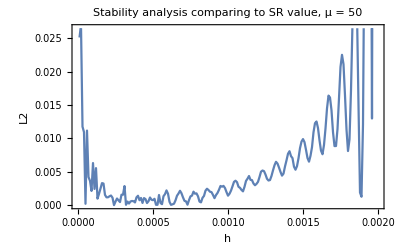

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9720983265536157)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 50 ", Frame->True, FrameLabel->{"h","L2"}]
```

### μ = 50 with other discretization of ϕ Max Step = 100

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.002, 0.00001}]];
```

InterpolatingFunction::dmval: Input value {-5469.96} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-2591.84} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-21.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == -176.679, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

```mathematica
ListPlot[sssa]
```

-Graphics-

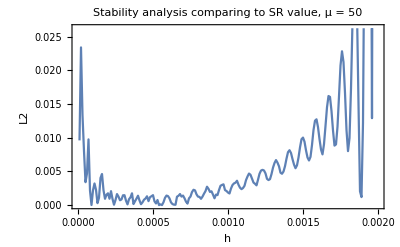

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9720983265536157)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 50 ", Frame->True, FrameLabel->{"h","L2"}]
```

### μ = 50 with other discretization of ϕ Max Step = 50

```mathematica
sssa = Parallelize[Table[{ h2 = i,nS[0.002] },{i, 0.00001, 0.002, 0.00001}]]
```

$Aborted

```mathematica
ListPlot[sssa]
```

-Graphics-

```mathematica
erro = Sqrt[(Transpose[sssa][[2]] -0.9720983265536157)^2];
ListPlot[Transpose[{Transpose[sssa][[1]],erro}],Joined->True,PlotLabel->"Stability analysis comparing to SR value, μ = 50 ", Frame->True, FrameLabel->{"h","L2"}]
```

-Graphics-